```mathematica
FindDirectRefinements[sets_]:=Block[{result={},pairs=Subsets[Range[Length[sets]],{2}], whereToGo,current},
Table[
whereToGo=Select[Range[Length[sets]],!MemberQ[p,#]&];
current=sets;
current=Drop[current,{p[[2]]}];
current=Drop[current,{p[[1]]}];
current=Append[current,Join[sets[[p[[1]]]],sets[[p[[2]]]]]];
current=Sort[Map[Sort[#]&,current],#1[[1]]<#2[[1]]&];
If[Length[current]==Length[sets]-1,
AppendTo[result,current]
]
,{p,pairs}
];
result
]
```

```mathematica
CalcClosure[g_]:=Block[{edges,formula, closure, result=Association[]},
edges=Sort[EdgeList[g]];
Monitor[
Graph[g,VertexLabels->"Name"]->
Table[With[{

contract =Graph[EdgeContract[g,e],VertexLabels->"Name",GraphHighlight->{e[[1]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding"]

},
formula=Map[SymbolReplace[#,e]&,FindFullFormula[contract]];
closure=Map[SetsToSymbol2,DeleteDuplicates[Flatten[Map[FindDirectRefinements  [SymbolToSets[#]]&,formula],1]]];
Table[
If[KeyExistsQ[result,new],
result[new]=Join[result[new],{e}],
result[new]={e}
]
,{new,SetDifference[closure,formula]}]
],{e,edges}],
e];
{edges,
result,
Length[result],
Length[FindFullFormula[g]],
FormulaGraphReverse2[Map[Plus,Keys[result]]],
FindFullFormula[g],

FormulaGraphReverse2[FindFullFormula[g]]}
]
```

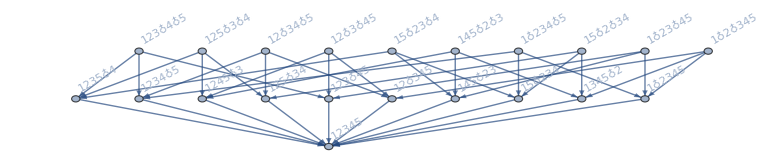
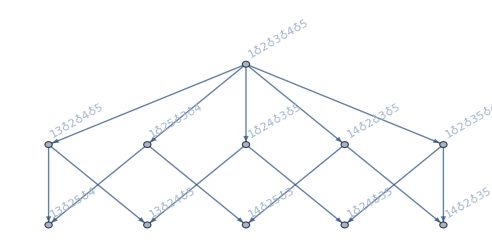
{{1<->2,1<->5,2<->3,3<->4,4<->5},<|v123x4x5→{1<->2,2<->3},v125x3x4→{1<->2,1<->5},v12x34x5→{1<->2,3<->4},v12x3x45→{1<->2,4<->5},v1234x5→{1<->2,2<->3,3<->4},v1245x3→{1<->2,1<->5,4<->5},v1235x4→{1<->2,1<->5,2<->3},v12x345→{1<->2},v12345→{1<->2,1<->5,2<->3,3<->4,4<->5},v145x2x3→{1<->5,4<->5},v15x23x4→{1<->5,2<->3},v15x2x34→{1<->5,3<->4},v1345x2→{1<->5,3<->4,4<->5},v15x234→{1<->5},v1x234x5→{2<->3,3<->4},v1x23x45→{2<->3,4<->5},v1x2345→{2<->3,3<->4,4<->5},v145x23→{2<->3},v1x2x345→{3<->4,4<->5},v125x34→{3<->4},v123x45→{4<->5}|>,21,11,-Graphics-,{v1x2x3x4x5,v1x2x35x4,v1x25x3x4,v1x24x3x5,v1x24x35,v14x2x3x5,v14x2x35,v14x25x3,v13x2x4x5,v13x25x4,v13x24x5},-Graphics-}

```mathematica
CalcClosure[CycleGraph[5]]
```